```mathematica
(*Time to solve over*)
tmax = 100.0;

(*Height*)
h = 100.0;
(*Kinematic Viscosity*)
ν = 1.0;
(*Acceleration due to gravity*)
g = 9.8;
(*Tilt Angle*)
α = Pi/4;

(*Differential Equation*)
NDSolve[{D[v[z,t],t]==ν*D[v[z,t],z,z]+g*Sin[α],
(*Initial Conditions*)
v[z,0]==0(*fluid is initially at rest*),
v[0,t]==0(*fluid has no velocity at the bottom of the plane*),
(D[v[z,t],z]/.z->0)==0(*free surface condition*)},
v,{t,0,tmax},{z,0,h}];

Plot3D[Evaluate[v[z,t]/.%],{t,0,tmax},{z,0,h},PlotRange->All,AxesLabel->{"Time", z, "Velocity"}]
```

-Graphics3D-

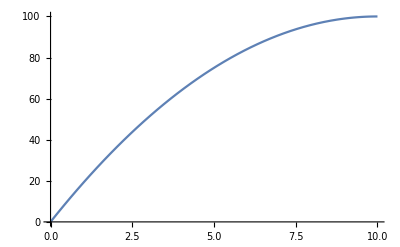

∫_(-∞)^∞ e^(-ι ω (t-t'))/(-ιω+(k^2 η)/ρ)ⅆt

```mathematica
Plot[z*(2h-z),{z,0,10}]
```